Your Title Here

```mathematica
Manipulate[
Module[{qgen,r1,ri,ro,Ti,To,Tx,q,p1,p2},
qgen=Hgen*1*^6;(*W/m3*)

r1=2;ri=r1/100;ro=r2/100;(*m*)

Ti=qgen/(2*h*ri)*(ro^2-ri^2)+T∞;
To=Ti-qgen/(4*k)*(ro^2-ri^2)+qgen/(2*k)*ro^2*Log[ro/ri];
Tx[x_]:=To+qgen/(4*k)*(ro^2-x^2)-qgen/(2*k)*ro^2*Log[ro/x];
q=-π*qgen*(ro^2-ri^2);

p2=Plot[Tx[x/100],{x,r1,r2},PlotStyle->{Thick,Black},PlotRange->{{r1,r2},{370,970}},PlotRangePadding->{None,Scaled@0.02},
Frame->True,FrameLabel->{"radius (cm)","temperature (K)"},LabelStyle->{17,Black},ImagePadding->{{65,15},{50,5}},
PlotLabel->Style[Row@{Style["T",Italic],"(",Style["r",Italic],") = ",IntegerPart@Tx[r/100]," K"},18],
Epilog->{PointSize@0.02,Point@{r,Tx[r/100]}}];

p1=RegionPlot[x^2+y^2≤(1.3*r2^2),{x,-3.4,3.4},{y,-3.4,3.4},Mesh->40,MeshFunctions->{#1-#2&},MeshShading->{None},BoundaryStyle->None,PerformanceGoal->"Quality",
PlotRange->{{-3.4,10},{-4.48,4.48}},Frame->False,
Epilog->{
{Yellow,Disk[{0,0},r2],RGBColor[0.65,0.75,1],Disk[{0,0},r1]},
{PointSize@0.007,Point[{0,0}],Point[{r1,0}],Point[r2*{Cos[15°],-Sin[15°]}]},
Style[#,20]&/@{
Text[Subscript[Style["T",Italic],#1],#2,{-1.2,0}]&@@@{{"∞",{0,0}},{"i",{r1,0}},{"o",r2*{Cos[15°],-Sin[15°]}}},
Text["insulation",√1.3*r2*{Cos[45°],Sin[45°]},{-1,0}],Text["coolant",{0,-r1/2}],
Text[Subscript[Style["r",Italic],"i"],{0,r1},{0,-1}],
Text[Subscript[Style["r",Italic],"o"],r2*{-Cos[60°],Sin[60°]},0.8*{1,-1}],
Text[Style["r",Italic],{-r,0},{1,0}]},
{Arrowheads@0.02,Arrow[{{0,0},r2*{-Cos[60°],Sin[60°]}}],Arrow[{{0,0},{-r,0}}],Arrow[{{0,0},{0,r1}}]},
Text[Style[Column[{
Row@{"heat transfer ",Superscript[Style["q",Italic],"′"],"(",Style["r",Italic],")"},Row@{NumberForm[N@q/1000,{5,2}]," kW/m"},Spacer@0,
Row@{"temperature ",Style["T",Italic],"(",Style["r",Italic],")"},Row@{IntegerPart@Tx[r/100]," K"},Spacer@0,
Row@{"outer surface temperature ",Subscript[Style["T",Italic],"o"]},Row@{IntegerPart@N@To," K"}
},Center],20],Scaled@{0.75,0.5}]
}];

Show[Switch[tap,1,p1,2,p2],ImageSize->{600,400},AspectRatio->Full]
],
Grid[{
{Control[{{tap,1,""},{1->" cylinder ",2->" temperature plot "},Setter}],
Control[{{Hgen,5,Row@{"heat generation (MW/",Superscript["m",3],")"}},2.5,5.5,0.5,Appearance-> "Labeled",ImageSize->Small}]},
{Row@{Control[{{r2,3,Row@{"thickness ",Subscript[Style["r",Italic],"o"]," - ",Subscript[Style["r",Italic],"i"]," (cm)"}},2.5,3,0.1,ImageSize->Small,TrackingFunction->(r2=#;r=N@(2+r2)/2;&)}],Spacer@5,Dynamic@NumberForm[N@(r2-2),{2,1}]},
Control[{{T∞,320,Row@{"coolant temperature ",Subscript[Style["T",Italic],"∞"]," (K)"}},300,420,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{r,2.2,Row@{"position ",Style["r",Italic]," (cm)"}},2,r2,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{h,180,Row@{"convection coefficient ",Style["h ",Italic],"(W/[",Superscript["m",2]," K])"}},150,200,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{k,5,Row@{"thermal conductivity ",Style["k",Italic]," (W/[m K])"}},3.5,7.5,0.5,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft}
},Alignment->Left]
]
```

```mathematica
Manipulate[
Module[{qgen,r1,ri,ro,Ti,To,Tx,q,p1,p2,p3},
qgen=Hgen*1*^6;(*W/m3*)

r1=2;ri=r1/100;ro=r2/100;(*m*)

Ti=qgen/(2*h*ri)*(ro^2-ri^2)+T∞;
To=Ti-qgen/(4*k)*(ro^2-ri^2)+qgen/(2*k)*ro^2*Log[ro/ri];
Tx[x_]:=To+qgen/(4*k)*(ro^2-x^2)-qgen/(2*k)*ro^2*Log[ro/x];
q=-π*qgen*(ro^2-ri^2);

p3=Plot[Tx[x/100],{x,r1,r2},PlotStyle->{Thick,Black},PlotRange->{{r1,r2},{370,970}},PlotRangePadding->{None,Scaled@0.02},
Frame->True,FrameLabel->{"radius (cm)","temperature (K)"},LabelStyle->{17,Black},ImageSize->{600,400},AspectRatio->Full,ImagePadding->{{65,15},{50,5}},
PlotLabel->Style[Row@{Style["T",Italic],"(",Style["r",Italic],") = ",IntegerPart@Tx[r/100]," K"},18],
Epilog->{PointSize@0.02,Point@{r,Tx[r/100]}}];

p1=RegionPlot[x^2+y^2≤(1.3*r2^2),{x,-3.4,3.4},{y,-3.4,3.4},Mesh->40,MeshFunctions->{#1-#2&},MeshShading->{None},BoundaryStyle->None,PerformanceGoal->"Quality",
PlotRange->{{-3.4,3.4},{-4.48,4.48}},Frame->False,ImageSize->{359,400},AspectRatio->1.3,
Epilog->{
{Yellow,Disk[{0,0},r2],RGBColor[0.65,0.75,1],Disk[{0,0},r1]},
{PointSize@0.007,Point[{0,0}],Point[{r1,0}],Point[r2*{Cos[15°],-Sin[15°]}]},
Style[#,20]&/@{
Text[Subscript[Style["T",Italic],#1],#2,{-1.2,0}]&@@@{{"∞",{0,0}},{"i",{r1,0}},{"o",r2*{Cos[15°],-Sin[15°]}}},
Text["insulation",√1.3*r2*{Cos[60°],Sin[60°]},{-1,0}],Text["coolant",{0,-r1/2}],
Text[Subscript[Style["r",Italic],"i"],{0,r1},{0,-1}],
Text[Subscript[Style["r",Italic],"o"],r2*{-Cos[60°],Sin[60°]},0.8*{1,-1}],
Text[Style["r",Italic],{-r,0},{1,0}]},
{Arrowheads@0.02,Arrow[{{0,0},r2*{-Cos[60°],Sin[60°]}}],Arrow[{{0,0},{-r,0}}],Arrow[{{0,0},{0,r1}}]}
}];

p2=Text@Style[Column[{
Row@{"heat transfer ",Superscript[Style["q",Italic],"′"],"(",Style["r",Italic],")"},Row@{NumberForm[N@q/1000,{5,2}]," kW/m"},Spacer@0,
Row@{"temperature ",Style["T",Italic],"(",Style["r",Italic],")"},Row@{IntegerPart@Tx[r/100]," K"},Spacer@0,
Row@{"outer surface temperature ",Subscript[Style["T",Italic],"o"]},Row@{IntegerPart@N@To," K"}
},Center],18];

Switch[tap,1,Grid@{{p1,p2}},2,p3]
],
Grid[{
{Control[{{tap,1,""},{1->" cylinder ",2->" temperature plot "},Setter}],
Control[{{Hgen,5,Row@{"heat generation (MW/",Superscript["m",3],")"}},2.5,5.5,0.5,Appearance-> "Labeled",ImageSize->Small}]},
{Row@{Control[{{r2,3,Row@{"thickness ",Subscript[Style["r",Italic],"o"]," - ",Subscript[Style["r",Italic],"i"]," (cm)"}},2.5,3,0.1,ImageSize->Small,TrackingFunction->(r2=#;r=N@(2+r2)/2;&)}],Spacer@5,Dynamic@NumberForm[N@(r2-2),{2,1}]},
Control[{{T∞,320,Row@{"coolant temperature ",Subscript[Style["T",Italic],"∞"]," (K)"}},300,420,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{r,2.2,Row@{"position ",Style["r",Italic]," (cm)"}},2,r2,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{h,180,Row@{"convection coefficient ",Style["h ",Italic],"(W/[",Superscript["m",2]," K])"}},150,200,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{k,5,Row@{"thermal conductivity ",Style["k",Italic]," (W/[m K])"}},3.5,7.5,0.5,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft}
},Alignment->Left]
]
```

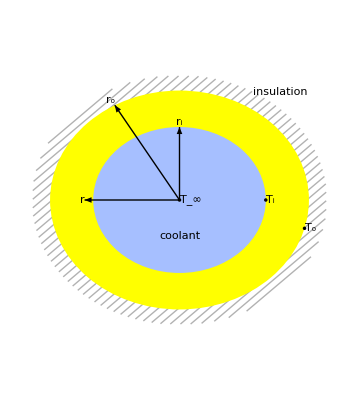
```mathematica
N@ImageAspectRatio@-Graphics-
```

1.11421





```mathematica
Text[Style[Column[{
Row@{"heat transfer ",Superscript[Style["q",Italic],"′"],"(",Style["r",Italic],")"},Row@{NumberForm[N@q/1000,{5,2}]," kW/m"},Spacer@0,
Row@{"temperature ",Style["T",Italic],"(",Style["r",Italic],")"},Row@{IntegerPart@Tx[r/100]," K"},Spacer@0,
Row@{"outer surface temperature ",Subscript[Style["T",Italic],"o"]},Row@{IntegerPart@N@To," K"}
},Center],20],Scaled@{0.75,0.5}]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX